### c)

```mathematica
Solve[x*(r-x)+h==0,x]
```

{{x→1/2 (r-√(4 h+r^2))},{x→1/2 (r+√(4 h+r^2))}}

```mathematica
Solve[D[x*(r-x)+h,x]==0,x]
```

{{x→r/2}}

```mathematica
x = r/2;
f = Solve[x*(r-x)+h==0,h]
```

{{h→-r^2/4}}

### a)

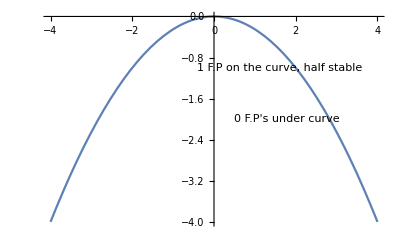

```mathematica
align[Right]={1,0};
align[Center]={0,0};
align[Left]={-1,0};

Text1=Text["0 F.P's under curve",{0.5,-2},align[Left]];
Text2=Text["1 F.P on the curve, half stable",{1.6,-1},align[Center]];
Text3=Text["2 F.P's above curve, 1 stable 1 unstable",{2.5,0.1},align[Right]];

txt=Graphics[{Text1,Text2,Text3}];
plot= Plot[-r^2/4,{r,-4,4}];

Show[plot,txt]
```

### b)

```mathematica
Clear[x]
Solve[x*(r-x)+h==0,r];
```

```mathematica
plot3 = ParametricPlot3D[{{r, h, 1/2(r+Sqrt[4h+r^2])}, {r, h, 1/2(r-Sqrt[4h+r^2])}}, {r, -3, 3}, {h, -3, 3}, PlotLegends->{"Positive roots", "Negative roots"}, {AxesLabel-> {r, h}}]
Show[plot3]
```

-Graphics3D-

-Graphics3D-

### d)

```mathematica
Solve[((r/2)^2-h)/(r/2)==0,h];
```

```mathematica
v = {-r^2/4,r};
v = D[v,r];
Normalize[v]
```

{-r/(2 √(1+Abs[r]^2/4)),1/(√(1+Abs[r]^2/4))}